/Users/eliasberriochoaesnaola

PolyLog[6,1/z]+PolyLog[6,z]

{Listable}

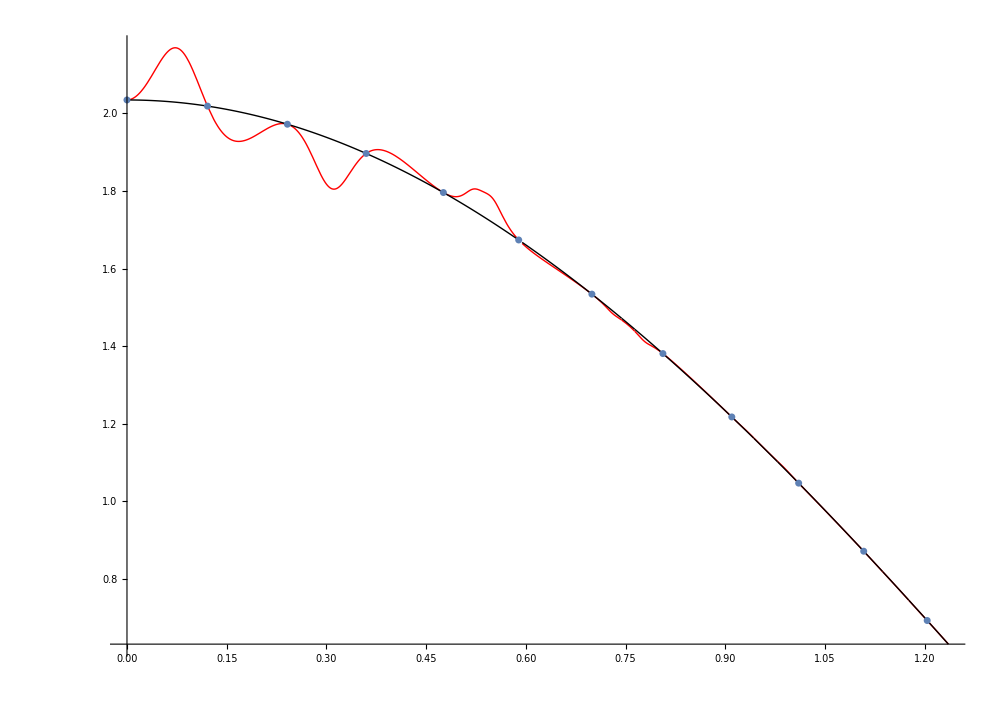

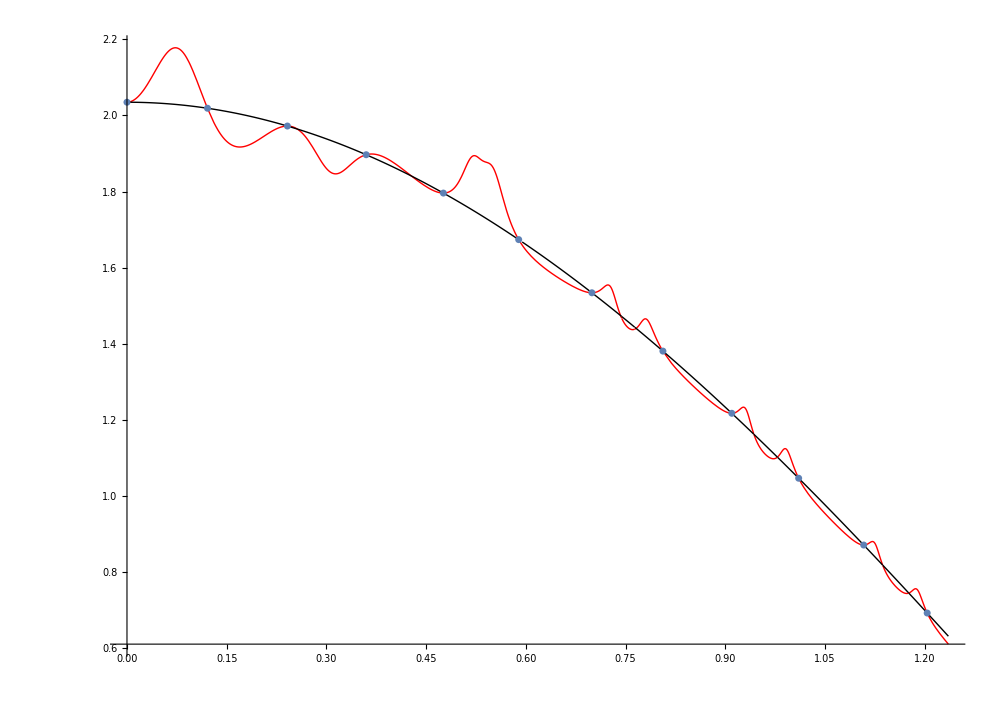

\text{Li}_6\left(\frac{1}{z}\right)+\text{Li}_6(z)

```mathematica
directorio=Directory[]

ftest[z_]=∑_(k=1)^∞ 1/k^6(z^k+z^(-k))
TeXForm[%]
 

Attributes[ftest]={Listable}



(* cardan.wls obtains the system of arcs related with the cardan device and write it as arcosalpha *)

n=30;T=2*Pi;betacardan=Pi/6;

Get["Dropbox/articulo2023/cardan.wls"]



(* arcos.wls obtains all the system of arcs related with arcosalpha in the sense of the paper and the related nodal systems *)
Get["Dropbox/atypeofinterpolation2023/arcos.wls"]

(* derivadas.wls obtains the derivatives used in the paper for a nodal system in T in this case for  alphaW2n nodal system *)
listaalpha=alphaW2n;listaarcosalpha=arcosalphaW2n;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaW2n=derivadas;
derivadassegundasalphaW2n=derivadas*factoresderivadassegundas;

(* same comment as before *)
listaalpha=alphaYn;listaarcosalpha=arcosalphaYn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaYn=derivadas;
derivadassegundasalphaYn=derivadas*factoresderivadassegundas;




(* same comment as before *)
listaalpha=alphaZn;listaarcosalpha=arcosalphaZn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaZn=derivadas;
derivadassegundasalphaZn=derivadas*factoresderivadassegundas;


(* u and v in the sense of the paper *)
u=ftest[alphaW2n];v=ftest'[alphaW2n];


(* semi Hermite and semi Hermite-Fejer interpolants using the barycentric formulae *)

SHFejer[z_]=(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]]u[[2k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)u[[2k-1]]))/(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)));

SHerm[z_]=(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]]u[[2k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)u[[2k-1]])+∑_(k=1)^n (alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]])v[[2k-1]]))/(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)));





BB=Plot[{Re[SHerm[E^(I x)]],Re[ftest[E^(I x)]]},{x,0,Pi/4+.45}, PlotRange->Full,PlotPoints->200,PlotStyle->{{Red,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7];
BB1=Plot[{Re[SHFejer[E^(I x)]],Re[ftest[E^(I x)]]},{x,0,Pi/4+.45}, PlotRange->Full,PlotPoints->200,PlotStyle->{{Red,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7];




AA=Table[{Re[Log[alphaW2n[[k]]]/I],Re[ftest[alphaW2n[[k]]]]},{k,1,2n}];
AA=ListPlot[AA,PlotStyle->PointSize[.005]];
Show[BB,AA]
Show[BB1,AA]
```